```mathematica
DIR="/home/rishi/work/sourendu/ankita/papers/NiharPaper/ankita_data_analysis/";
```

### 0-10 pct

```mathematica
Import[StringJoin[DIR,"tab1.csv"]];
```

Data contained in rows 14 to 18 of the tables.

```mathematica
Clear[n]
```

```mathematica
bin1=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->16}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{350.,300,400,0.645,0.016,-0.016,0.028,-0.028,0.065,-0.065,0.015,-0.015},{350.,300,400,0.657,0.015,-0.015,0.032,-0.032,0.066,-0.066,0.015,-0.015},{350.,300,400,-,0,0,0,0,0,0,0,0},{350.,300,400,-,0,0,0,0,0,0,0,0},{350.,300,400,-,0,0,0,0,0,0,0,0},{350.,300,400,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval1=Transpose[{{0.2,0.3},Table[bin1[[i,4]],{i,1,2}]}]
```

{{0.2,0.645},{0.3,0.657}}

```mathematica
err1=Table[Mean[Table[bin1[[i,n]],{n,5,11,2}]],{i,1,2}]
```

{0.031,0.032}

```mathematica
Needs["ErrorBarPlots`"]
```

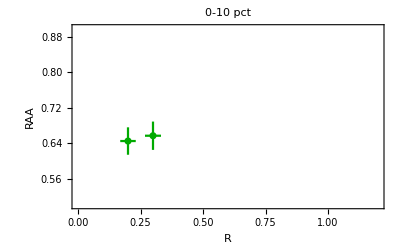

```mathematica
dat1=ErrorListPlot[{{centralval1[[1]],ErrorBar[err1[[1]],err1[[1]]]},{centralval1[[2]],ErrorBar[err1[[2]],err1[[2]]]}},PlotRange->{{0,1.2},{0.5,0.9}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Darker[Green],ImageSize->400,PlotLegends->Legended[Darker[Green],"300<pT<400"],PlotLabel->"0-10 pct"]
```

```mathematica
bin2=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->17}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{450.,400,500,0.672,0.043,-0.043,0.029,-0.029,0.068,-0.068,0.015,-0.015},{450.,400,500,0.697,0.04,-0.04,0.029,-0.029,0.07,-0.07,0.016,-0.016},{450.,400,500,0.704,0.037,-0.037,0.03,-0.03,0.071,-0.071,0.016,-0.016},{450.,400,500,0.74,0.035,-0.035,0.059,-0.059,0.075,-0.075,0.017,-0.017},{450.,400,500,0.75,0.03,-0.03,0.11,-0.11,0.08,-0.08,0.02,-0.02},{450.,400,500,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval2=Transpose[{{0.2,0.3,0.4,0.6,0.8},Table[bin2[[i,4]],{i,1,5}]}]
```

{{0.2,0.672},{0.3,0.697},{0.4,0.704},{0.6,0.74},{0.8,0.75}}

```mathematica
err2=Table[Mean[Table[bin2[[i,n]],{n,5,11,2}]],{i,1,5}]
```

{0.03875,0.03875,0.0385,0.0465,0.06}

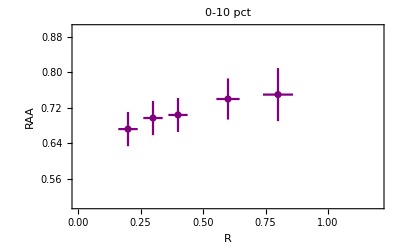

```mathematica
dat2=ErrorListPlot[{{centralval2[[1]],ErrorBar[err2[[1]],err2[[1]]]},{centralval2[[2]],ErrorBar[err2[[2]],err2[[2]]]},{centralval2[[3]],ErrorBar[err2[[3]],err2[[3]]]},{centralval2[[4]],ErrorBar[err2[[4]],err2[[4]]]},{centralval2[[5]],ErrorBar[err2[[5]],err2[[5]]]}},PlotRange->{{0,1.2},{0.5,0.9}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Purple,ImageSize->400,PlotLegends->Legended[Purple,"400<pT<500"],PlotLabel->"0-10 pct"]
```

```mathematica
bin3=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->18}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{750.,500,1000,0.796,0.09,-0.09,0.031,-0.031,0.08,-0.08,0.018,-0.018},{750.,500,1000,0.794,0.083,-0.083,0.028,-0.028,0.08,-0.08,0.018,-0.018},{750.,500,1000,0.742,0.074,-0.074,0.032,-0.032,0.075,-0.075,0.017,-0.017},{750.,500,1000,0.754,0.069,-0.069,0.044,-0.044,0.076,-0.076,0.017,-0.017},{750.,500,1000,0.786,0.067,-0.067,0.058,-0.058,0.079,-0.079,0.018,-0.018},{750.,500,1000,0.815,0.065,-0.065,0.094,-0.094,0.082,-0.082,0.019,-0.019}}

```mathematica
centralval3=Transpose[{{0.2,0.3,0.4,0.6,0.8,1.0},Table[bin3[[i,4]],{i,1,6}]}]
```

{{0.2,0.796},{0.3,0.794},{0.4,0.742},{0.6,0.754},{0.8,0.786},{1.,0.815}}

```mathematica
err3=Table[Mean[Table[bin3[[i,n]],{n,5,11,2}]],{i,1,6}]
```

{0.05475,0.05225,0.0495,0.0515,0.0555,0.065}

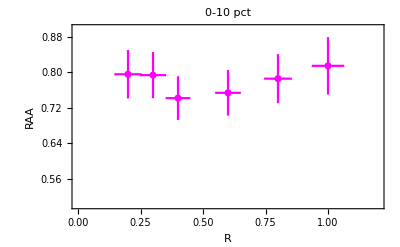

```mathematica
dat3=ErrorListPlot[{{centralval3[[1]],ErrorBar[err3[[1]],err3[[1]]]},{centralval3[[2]],ErrorBar[err3[[2]],err3[[2]]]},{centralval3[[3]],ErrorBar[err3[[3]],err3[[3]]]},{centralval3[[4]],ErrorBar[err3[[4]],err3[[4]]]},{centralval3[[5]],ErrorBar[err3[[5]],err3[[5]]]},{centralval3[[6]],ErrorBar[err3[[6]],err3[[6]]]}},PlotRange->{{0,1.2},{0.5,0.9}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Magenta,ImageSize->400,PlotLegends->Legended[Magenta,"500<pT<1000"],PlotLabel->"0-10 pct"]
```

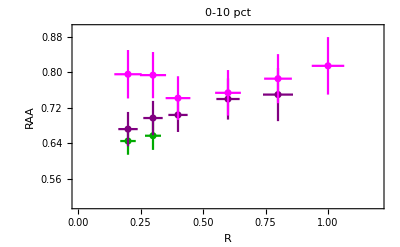

```mathematica
Show[{dat1,dat2,dat3}]
```

```mathematica
fit10c34={0.65,0.01, 0.93};
fit10c45={0.71,0.02, 0.63};
fit10c50={0.78,0.01, 0.43};
```

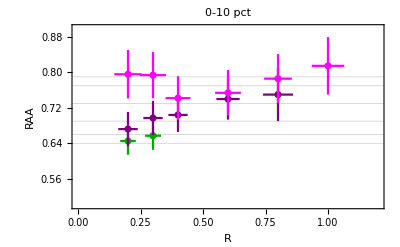

```mathematica
Show[{dat1,dat2,dat3},GridLines->{None,{{fit10c34[[1]]+fit10c34[[2]],{Darker[Green],Thick}},{fit10c34[[1]]-fit10c34[[2]],{Darker[Green],Thick}},{fit10c45[[1]]+fit10c45[[2]],{Purple,Thick}},{fit10c45[[1]]-fit10c45[[2]],{Purple,Thick}},{fit10c50[[1]]+fit10c50[[2]],{Magenta,Thick}},{fit10c50[[1]]-fit10c50[[2]],{Magenta,Thick}}}}]
```

### 10-30 pct

Data contained in rows 26 to 30 of the tables.

```mathematica
bin11=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->26}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{225.,200,250,0.698,0.006,-0.006,0.037,-0.037,0.036,-0.036,0.016,-0.016},{225.,200,250,0.702,0.005,-0.005,0.033,-0.033,0.036,-0.036,0.016,-0.016},{225.,200,250,-,0,0,0,0,0,0,0,0},{225.,200,250,-,0,0,0,0,0,0,0,0},{225.,200,250,-,0,0,0,0,0,0,0,0},{225.,200,250,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval11=Transpose[{{0.2,0.3},Table[bin11[[i,4]],{i,1,2}]}]
```

{{0.2,0.698},{0.3,0.702}}

```mathematica
err11=Table[Mean[Table[bin11[[i,n]],{n,5,11,2}]],{i,1,2}]
```

{0.02375,0.0225}

```mathematica
Needs["ErrorBarPlots`"]
```

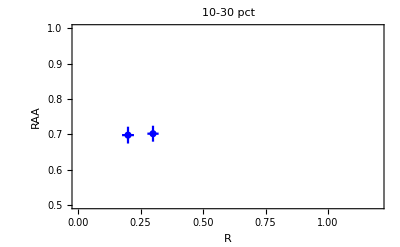

```mathematica
dat11=ErrorListPlot[{{centralval11[[1]],ErrorBar[err11[[1]],err11[[1]]]},{centralval11[[2]],ErrorBar[err11[[2]],err11[[2]]]}},PlotRange->{{0,1.2},{0.5,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Blue,ImageSize->400,PlotLegends->Legended[Blue,"200<pT<250"],PlotLabel->"10-30 pct"]
```

```mathematica
bin12=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->27}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{275.,250,300,0.714,0.012,-0.012,0.034,-0.034,0.037,-0.037,0.016,-0.016},{275.,250,300,0.729,0.011,-0.011,0.032,-0.032,0.037,-0.037,0.017,-0.017},{275.,250,300,-,0,0,0,0,0,0,0,0},{275.,250,300,-,0,0,0,0,0,0,0,0},{275.,250,300,-,0,0,0,0,0,0,0,0},{275.,250,300,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval12=Transpose[{{0.2,0.3},Table[bin12[[i,4]],{i,1,2}]}]
```

{{0.2,0.714},{0.3,0.729}}

```mathematica
err12=Table[Mean[Table[bin12[[i,n]],{n,5,11,2}]],{i,1,2}]
```

{0.02475,0.02425}

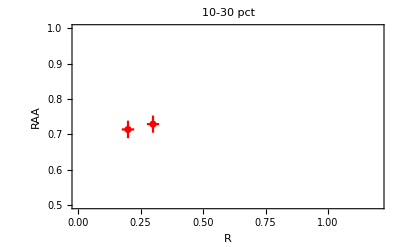

```mathematica
dat12=ErrorListPlot[{{centralval12[[1]],ErrorBar[err12[[1]],err12[[1]]]},{centralval12[[2]],ErrorBar[err12[[2]],err12[[2]]]}},PlotRange->{{0,1.2},{0.5,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Red,ImageSize->400,PlotLegends->Legended[Red,"250<pT<300"],PlotLabel->"10-30 pct"]
```

```mathematica
bin13=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->28}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{350.,300,400,0.728,0.017,-0.017,0.026,-0.026,0.037,-0.037,0.017,-0.017},{350.,300,400,0.745,0.016,-0.016,0.027,-0.027,0.038,-0.038,0.017,-0.017},{350.,300,400,0.707,0.014,-0.014,0.039,-0.039,0.036,-0.036,0.016,-0.016},{350.,300,400,0.758,0.014,-0.014,0.051,-0.051,0.039,-0.039,0.017,-0.017},{350.,300,400,-,0,0,0,0,0,0,0,0},{350.,300,400,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval13=Transpose[{{0.2,0.3,0.4,0.6},Table[bin13[[i,4]],{i,1,4}]}]
```

{{0.2,0.728},{0.3,0.745},{0.4,0.707},{0.6,0.758}}

```mathematica
err13=Table[Mean[Table[bin13[[i,n]],{n,5,11,2}]],{i,1,4}]
```

{0.02425,0.0245,0.02625,0.03025}

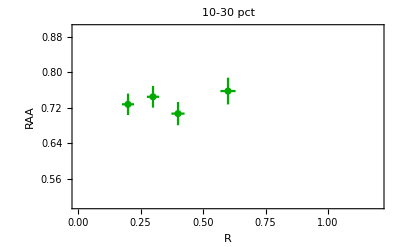

```mathematica
dat13=ErrorListPlot[{{centralval13[[1]],ErrorBar[err13[[1]],err13[[1]]]},{centralval13[[2]],ErrorBar[err13[[2]],err13[[2]]]},{centralval13[[3]],ErrorBar[err13[[3]],err13[[3]]]},{centralval13[[4]],ErrorBar[err13[[4]],err13[[4]]]}},PlotRange->{{0,1.2},{0.5,0.9}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Darker[Green],ImageSize->400,PlotLegends->Legended[Darker[Green],"300<pT<400"],PlotLabel->"10-30 pct"]
```

```mathematica
bin13=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->28}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{350.,300,400,0.728,0.017,-0.017,0.026,-0.026,0.037,-0.037,0.017,-0.017},{350.,300,400,0.745,0.016,-0.016,0.027,-0.027,0.038,-0.038,0.017,-0.017},{350.,300,400,0.707,0.014,-0.014,0.039,-0.039,0.036,-0.036,0.016,-0.016},{350.,300,400,0.758,0.014,-0.014,0.051,-0.051,0.039,-0.039,0.017,-0.017},{350.,300,400,-,0,0,0,0,0,0,0,0},{350.,300,400,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval13=Transpose[{{0.2,0.3,0.4,0.6},Table[bin13[[i,4]],{i,1,4}]}]
```

{{0.2,0.728},{0.3,0.745},{0.4,0.707},{0.6,0.758}}

```mathematica
err13=Table[Mean[Table[bin13[[i,n]],{n,5,11,2}]],{i,1,4}]
```

{0.02425,0.0245,0.02625,0.03025}

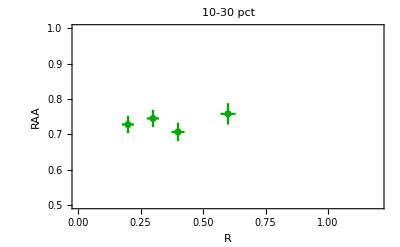

```mathematica
dat13=ErrorListPlot[{{centralval13[[1]],ErrorBar[err13[[1]],err13[[1]]]},{centralval13[[2]],ErrorBar[err13[[2]],err13[[2]]]},{centralval13[[3]],ErrorBar[err13[[3]],err13[[3]]]},{centralval13[[4]],ErrorBar[err13[[4]],err13[[4]]]}},PlotRange->{{0,1.2},{0.5,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Darker[Green],ImageSize->400,PlotLegends->Legended[Darker[Green],"300<pT<400"],PlotLabel->"10-30 pct"]
```

```mathematica
bin14=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->29}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{450.,400,500,0.649,0.042,-0.042,0.019,-0.019,0.033,-0.033,0.015,-0.015},{450.,400,500,0.651,0.038,-0.038,0.022,-0.022,0.033,-0.033,0.015,-0.015},{450.,400,500,0.696,0.037,-0.037,0.033,-0.033,0.036,-0.036,0.016,-0.016},{450.,400,500,0.708,0.035,-0.035,0.045,-0.045,0.036,-0.036,0.016,-0.016},{450.,400,500,0.793,0.035,-0.035,0.07,-0.07,0.041,-0.041,0.018,-0.018},{450.,400,500,0.77,0.03,-0.03,0.11,-0.11,0.04,-0.04,0.02,-0.02}}

```mathematica
centralval14=Transpose[{{0.2,0.3,0.4,0.6,0.8,1.0},Table[bin14[[i,4]],{i,1,6}]}]
```

{{0.2,0.649},{0.3,0.651},{0.4,0.696},{0.6,0.708},{0.8,0.793},{1.,0.77}}

```mathematica
err14=Table[Mean[Table[bin14[[i,n]],{n,5,11,2}]],{i,1,6}]
```

{0.02725,0.027,0.0305,0.033,0.041,0.05}

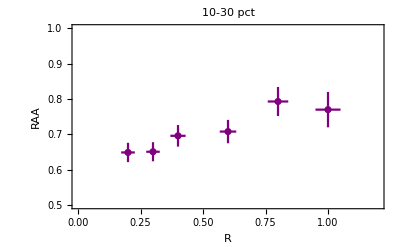

```mathematica
dat14=ErrorListPlot[{{centralval14[[1]],ErrorBar[err14[[1]],err14[[1]]]},{centralval14[[2]],ErrorBar[err14[[2]],err14[[2]]]},{centralval14[[3]],ErrorBar[err14[[3]],err14[[3]]]},{centralval14[[4]],ErrorBar[err14[[4]],err14[[4]]]},{centralval14[[5]],ErrorBar[err14[[5]],err14[[5]]]},{centralval14[[6]],ErrorBar[err14[[6]],err14[[6]]]}},PlotRange->{{0,1.2},{0.5,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Purple,ImageSize->400,PlotLegends->Legended[Purple,"400<pT<500"],PlotLabel->"10-30 pct"]
```

```mathematica
bin15=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->30}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{750.,500,1000,0.935,0.099,-0.099,0.025,-0.025,0.048,-0.048,0.022,-0.022},{750.,500,1000,0.856,0.087,-0.087,0.032,-0.032,0.044,-0.044,0.02,-0.02},{750.,500,1000,0.825,0.079,-0.079,0.037,-0.037,0.042,-0.042,0.019,-0.019},{750.,500,1000,0.804,0.072,-0.072,0.049,-0.049,0.041,-0.041,0.018,-0.018},{750.,500,1000,0.765,0.066,-0.066,0.036,-0.036,0.039,-0.039,0.018,-0.018},{750.,500,1000,0.77,0.063,-0.063,0.061,-0.061,0.039,-0.039,0.018,-0.018}}

```mathematica
centralval15=Transpose[{{0.2,0.3,0.4,0.6,0.8,1.0},Table[bin15[[i,4]],{i,1,6}]}]
```

{{0.2,0.935},{0.3,0.856},{0.4,0.825},{0.6,0.804},{0.8,0.765},{1.,0.77}}

```mathematica
err15=Table[Mean[Table[bin15[[i,n]],{n,5,11,2}]],{i,1,6}]
```

{0.0485,0.04575,0.04425,0.045,0.03975,0.04525}

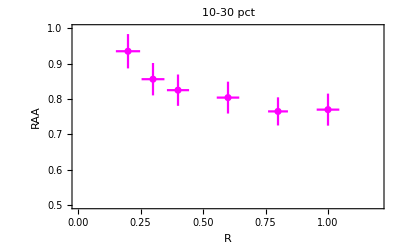

```mathematica
dat15=ErrorListPlot[{{centralval15[[1]],ErrorBar[err15[[1]],err15[[1]]]},{centralval15[[2]],ErrorBar[err15[[2]],err15[[2]]]},{centralval15[[3]],ErrorBar[err15[[3]],err15[[3]]]},{centralval15[[4]],ErrorBar[err15[[4]],err15[[4]]]},{centralval15[[5]],ErrorBar[err15[[5]],err15[[5]]]},{centralval15[[6]],ErrorBar[err15[[6]],err15[[6]]]}},PlotRange->{{0,1.2},{0.5,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Magenta,ImageSize->400,PlotLegends->Legended[Magenta,"500<pT<1000"],PlotLabel->"10-30 pct"]
```

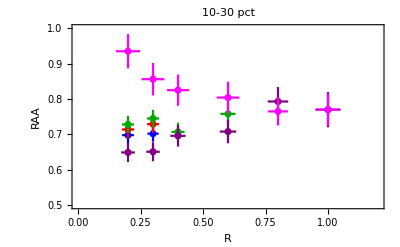

```mathematica
Show[{dat11,dat12,dat13,dat14,dat15}]
```

```mathematica
fit30c22={0.7, 0.003, 0.99};
fit30c23={0.72, 0.01, 0.88};
fit30c34={0.73, 0.01, 0.75};
fit30c45={0.69, 0.02, 2.71};
fit30c50={0.82, 0.03, 1.9};
```

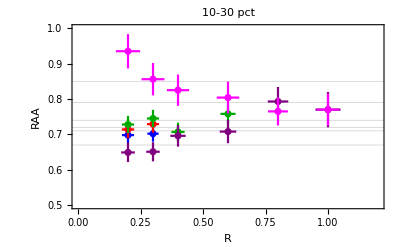

```mathematica
Show[{dat11,dat12,dat13,dat14,dat15},GridLines->{None,{{fit30c34[[1]]+fit30c34[[2]],{Darker[Green],Thick}},{fit30c34[[1]]-fit30c34[[2]],{Darker[Green],Thick}},{fit30c45[[1]]+fit30c45[[2]],{Purple,Thick}},{fit30c45[[1]]-fit30c45[[2]],{Purple,Thick}},{fit30c50[[1]]+fit30c50[[2]],{Magenta,Thick}},{fit30c50[[1]]-fit30c50[[2]],{Magenta,Thick}}}}]
```

### 30-50 pct

Data contained in rows 38 to 42 of the tables.

```mathematica
bin21=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->38}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{225.,200,250,0.795,0.011,-0.011,0.033,-0.033,0.02,-0.02,0.018,-0.018},{225.,200,250,0.797,0.01,-0.01,0.03,-0.03,0.02,-0.02,0.018,-0.018},{225.,200,250,-,0,0,0,0,0,0,0,0},{225.,200,250,-,0,0,0,0,0,0,0,0},{225.,200,250,-,0,0,0,0,0,0,0,0},{225.,200,250,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval21=Transpose[{{0.2,0.3},Table[bin21[[i,4]],{i,1,2}]}]
```

{{0.2,0.795},{0.3,0.797}}

```mathematica
err21=Table[Mean[Table[bin21[[i,n]],{n,5,11,2}]],{i,1,2}]
```

{0.0205,0.0195}

```mathematica
Needs["ErrorBarPlots`"]
```

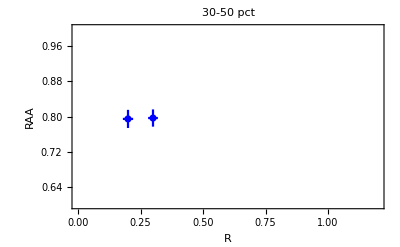

```mathematica
dat21=ErrorListPlot[{{centralval21[[1]],ErrorBar[err21[[1]],err21[[1]]]},{centralval21[[2]],ErrorBar[err21[[2]],err21[[2]]]}},PlotRange->{{0,1.2},{0.6,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Blue,ImageSize->400,PlotLegends->Legended[Blue,"200<pT<250"],PlotLabel->"30-50 pct"]
```

```mathematica
bin22=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->39}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{275.,250,300,0.812,0.021,-0.021,0.034,-0.034,0.021,-0.021,0.019,-0.019},{275.,250,300,0.814,0.019,-0.019,0.026,-0.026,0.021,-0.021,0.019,-0.019},{275.,250,300,0.776,0.017,-0.017,0.034,-0.034,0.02,-0.02,0.018,-0.018},{275.,250,300,0.851,0.016,-0.016,0.045,-0.045,0.022,-0.022,0.02,-0.02},{275.,250,300,0.848,0.015,-0.015,0.056,-0.056,0.021,-0.021,0.02,-0.02},{275.,250,300,0.89,0.014,-0.014,0.046,-0.046,0.023,-0.023,0.02,-0.02}}

```mathematica
centralval22=Transpose[{{0.2,0.3,0.4,0.6,0.8,1.0},Table[bin22[[i,4]],{i,1,6}]}]
```

{{0.2,0.812},{0.3,0.814},{0.4,0.776},{0.6,0.851},{0.8,0.848},{1.,0.89}}

```mathematica
err22=Table[Mean[Table[bin22[[i,n]],{n,5,11,2}]],{i,1,6}]
```

{0.02375,0.02125,0.02225,0.02575,0.028,0.02575}

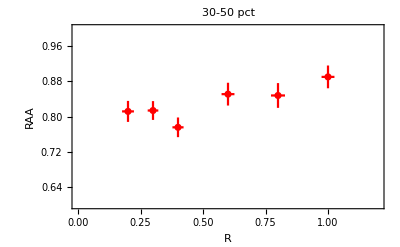

```mathematica
dat22=ErrorListPlot[{{centralval22[[1]],ErrorBar[err22[[1]],err22[[1]]]},{centralval22[[2]],ErrorBar[err22[[2]],err22[[2]]]},{centralval22[[3]],ErrorBar[err22[[3]],err22[[3]]]},{centralval22[[4]],ErrorBar[err22[[4]],err22[[4]]]},{centralval22[[5]],ErrorBar[err22[[5]],err22[[5]]]},{centralval22[[6]],ErrorBar[err22[[6]],err22[[6]]]}},PlotRange->{{0,1.2},{0.6,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Red,ImageSize->400,PlotLegends->Legended[Red,"250<pT<300"],PlotLabel->"30-50 pct"]
```

```mathematica
bin23=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->40}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{350.,300,400,0.883,0.032,-0.032,0.031,-0.031,0.022,-0.022,0.02,-0.02},{350.,300,400,0.881,0.029,-0.029,0.023,-0.023,0.022,-0.022,0.02,-0.02},{350.,300,400,0.844,0.026,-0.026,0.024,-0.024,0.021,-0.021,0.019,-0.019},{350.,300,400,0.854,0.024,-0.024,0.022,-0.022,0.022,-0.022,0.02,-0.02},{350.,300,400,0.873,0.023,-0.023,0.034,-0.034,0.022,-0.022,0.02,-0.02},{350.,300,400,0.849,0.021,-0.021,0.036,-0.036,0.022,-0.022,0.02,-0.02}}

```mathematica
centralval23=Transpose[{{0.2,0.3,0.4,0.6,0.8,1.0},Table[bin23[[i,4]],{i,1,6}]}]
```

{{0.2,0.883},{0.3,0.881},{0.4,0.844},{0.6,0.854},{0.8,0.873},{1.,0.849}}

```mathematica
err23=Table[Mean[Table[bin23[[i,n]],{n,5,11,2}]],{i,1,6}]
```

{0.02625,0.0235,0.0225,0.022,0.02475,0.02475}

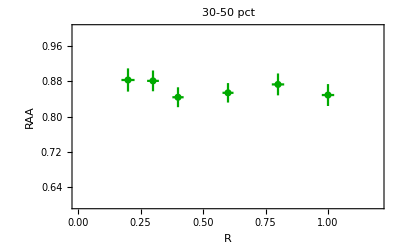

```mathematica
dat23=ErrorListPlot[{{centralval23[[1]],ErrorBar[err23[[1]],err23[[1]]]},{centralval23[[2]],ErrorBar[err23[[2]],err23[[2]]]},{centralval23[[3]],ErrorBar[err23[[3]],err23[[3]]]},{centralval23[[4]],ErrorBar[err23[[4]],err23[[4]]]},{centralval23[[5]],ErrorBar[err23[[5]],err23[[5]]]},{centralval23[[6]],ErrorBar[err23[[6]],err23[[6]]]}},PlotRange->{{0,1.2},{0.6,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Darker[Green],ImageSize->400,PlotLegends->Legended[Darker[Green],"300<pT<400"],PlotLabel->"30-50 pct"]
```

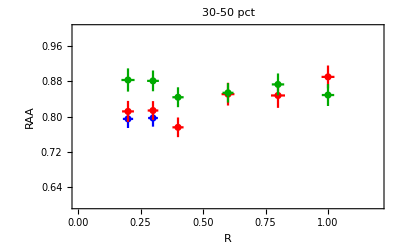

```mathematica
Show[{dat21,dat22,dat23}]
```

```mathematica
fit50c22={0.8, 0.002, 0.99};
fit50c23={0.82, 0.02, 2.69};
fit50c34={0.86, 0.007, 0.51};
```

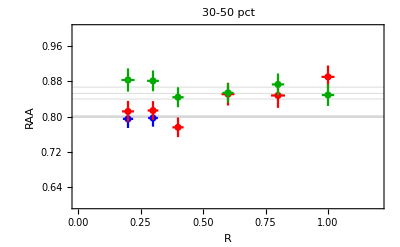

```mathematica
Show[{dat21,dat22,dat23},GridLines->{None,{{fit50c34[[1]]+fit50c34[[2]],{Darker[Green],Thick}},{fit50c34[[1]]-fit50c34[[2]],{Darker[Green],Thick}},{fit50c22[[1]]+fit50c22[[2]],{Blue,Thick}},{fit50c22[[1]]-fit50c22[[2]],{Blue,Thick}},{fit50c23[[1]]+fit50c23[[2]],{Red,Thick}},{fit50c23[[1]]-fit50c23[[2]],{Red,Thick}}}}]
```

### 50-90 pct

Data contained in rows 50 to 54 of the tables.

```mathematica
bin31=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->50}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{225.,200,250,0.85,0.021,-0.021,0.034,-0.034,0.016,-0.016,0.02,-0.02},{225.,200,250,0.858,0.018,-0.018,0.039,-0.039,0.016,-0.016,0.02,-0.02},{225.,200,250,0.802,0.016,-0.016,0.034,-0.034,0.015,-0.015,0.018,-0.018},{225.,200,250,0.869,0.016,-0.016,0.025,-0.025,0.016,-0.016,0.02,-0.02},{225.,200,250,-,0,0,0,0,0,0,0,0},{225.,200,250,-,0,0,0,0,0,0,0,0}}

```mathematica
centralval31=Transpose[{{0.2,0.3,0.4,0.6},Table[bin31[[i,4]],{i,1,4}]}]
```

{{0.2,0.85},{0.3,0.858},{0.4,0.802},{0.6,0.869}}

```mathematica
err31=Table[Mean[Table[bin31[[i,n]],{n,5,11,2}]],{i,1,4}]
```

{0.02275,0.02325,0.02075,0.01925}

```mathematica
Needs["ErrorBarPlots`"]
```

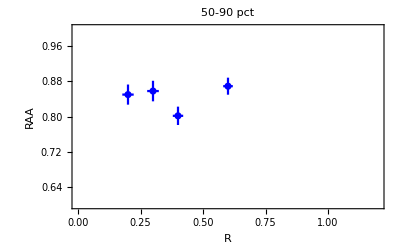

```mathematica
dat31=ErrorListPlot[{{centralval31[[1]],ErrorBar[err31[[1]],err31[[1]]]},{centralval31[[2]],ErrorBar[err31[[2]],err31[[2]]]},{centralval31[[3]],ErrorBar[err31[[3]],err31[[3]]]},{centralval31[[4]],ErrorBar[err31[[4]],err31[[4]]]}},PlotRange->{{0,1.2},{0.6,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Blue,ImageSize->400,PlotLegends->Legended[Blue,"200<pT<250"],PlotLabel->"50-90 pct"]
```

```mathematica
bin32=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->51}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{275.,250,300,0.844,0.038,-0.038,0.032,-0.032,0.016,-0.016,0.019,-0.019},{275.,250,300,0.832,0.034,-0.034,0.036,-0.036,0.016,-0.016,0.019,-0.019},{275.,250,300,0.812,0.031,-0.031,0.032,-0.032,0.015,-0.015,0.019,-0.019},{275.,250,300,0.863,0.03,-0.03,0.024,-0.024,0.016,-0.016,0.02,-0.02},{275.,250,300,0.852,0.027,-0.027,0.039,-0.039,0.016,-0.016,0.02,-0.02},{275.,250,300,0.857,0.026,-0.026,0.043,-0.043,0.016,-0.016,0.02,-0.02}}

```mathematica
centralval32=Transpose[{{0.2,0.3,0.4,0.6,0.8,1.0},Table[bin32[[i,4]],{i,1,6}]}]
```

{{0.2,0.844},{0.3,0.832},{0.4,0.812},{0.6,0.863},{0.8,0.852},{1.,0.857}}

```mathematica
err32=Table[Mean[Table[bin32[[i,n]],{n,5,11,2}]],{i,1,6}]
```

{0.02625,0.02625,0.02425,0.0225,0.0255,0.02625}

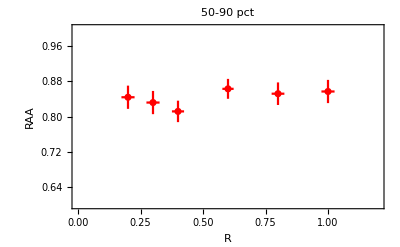

```mathematica
dat32=ErrorListPlot[{{centralval32[[1]],ErrorBar[err32[[1]],err32[[1]]]},{centralval32[[2]],ErrorBar[err32[[2]],err32[[2]]]},{centralval32[[3]],ErrorBar[err32[[3]],err32[[3]]]},{centralval32[[4]],ErrorBar[err32[[4]],err32[[4]]]},{centralval32[[5]],ErrorBar[err32[[5]],err32[[5]]]},{centralval32[[6]],ErrorBar[err32[[6]],err32[[6]]]}},PlotRange->{{0,1.2},{0.6,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Red,ImageSize->400,PlotLegends->Legended[Red,"250<pT<300"],PlotLabel->"50-90 pct"]
```

```mathematica
bin33=Join[{Import[StringJoin[DIR,"tab1.csv"]][[n]],Import[StringJoin[DIR,"tab2.csv"]][[n]],Import[StringJoin[DIR,"tab3.csv"]][[n]],Import[StringJoin[DIR,"tab4.csv"]][[n]],Import[StringJoin[DIR,"tab5.csv"]][[n]],Import[StringJoin[DIR,"tab6.csv"]][[n]]}]/.{n->52}
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{350.,300,400,0.849,0.057,-0.057,0.031,-0.031,0.016,-0.016,0.02,-0.02},{350.,300,400,0.836,0.052,-0.052,0.036,-0.036,0.016,-0.016,0.019,-0.019},{350.,300,400,0.825,0.047,-0.047,0.031,-0.031,0.015,-0.015,0.019,-0.019},{350.,300,400,0.864,0.045,-0.045,0.024,-0.024,0.016,-0.016,0.02,-0.02},{350.,300,400,0.848,0.041,-0.041,0.023,-0.023,0.016,-0.016,0.02,-0.02},{350.,300,400,0.868,0.039,-0.039,0.022,-0.022,0.016,-0.016,0.02,-0.02}}

```mathematica
centralval33=Transpose[{{0.2,0.3,0.4,0.6,0.8,1.0},Table[bin33[[i,4]],{i,1,6}]}]
```

{{0.2,0.849},{0.3,0.836},{0.4,0.825},{0.6,0.864},{0.8,0.848},{1.,0.868}}

```mathematica
err33=Table[Mean[Table[bin33[[i,n]],{n,5,11,2}]],{i,1,6}]
```

{0.031,0.03075,0.028,0.02625,0.025,0.02425}

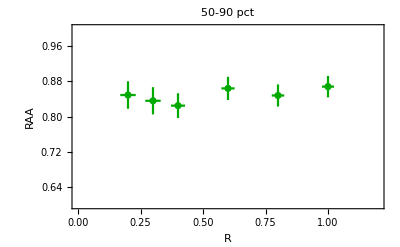

```mathematica
dat33=ErrorListPlot[{{centralval33[[1]],ErrorBar[err33[[1]],err33[[1]]]},{centralval33[[2]],ErrorBar[err33[[2]],err33[[2]]]},{centralval33[[3]],ErrorBar[err33[[3]],err33[[3]]]},{centralval33[[4]],ErrorBar[err33[[4]],err33[[4]]]},{centralval33[[5]],ErrorBar[err33[[5]],err33[[5]]]},{centralval33[[6]],ErrorBar[err33[[6]],err33[[6]]]}},PlotRange->{{0,1.2},{0.6,1.0}},Frame->True,FrameLabel->{Style["R",14],Style["RAA",14]},PlotStyle->Darker[Green],ImageSize->400,PlotLegends->Legended[Darker[Green],"300<pT<400"],PlotLabel->"50-90 pct"]
```

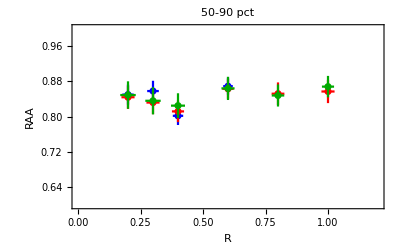

```mathematica
Show[{dat31,dat32,dat33}]
```

```mathematica
fit90c22={0.85, 0.02, 2.07};
fit90c23={0.84, 0.009, 0.61};
fit90c34={0.85, 0.007, 0.75};
```

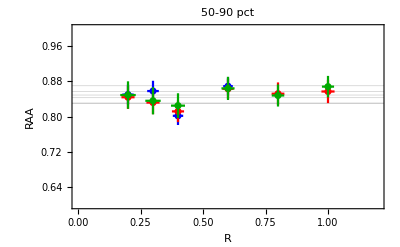

```mathematica
Show[{dat31,dat32,dat33},GridLines->{None,{{fit90c34[[1]]+fit90c34[[2]],{Darker[Green],Thick}},{fit90c34[[1]]-fit90c34[[2]],{Darker[Green],Thick}},{fit90c22[[1]]+fit90c22[[2]],{Blue,Thick}},{fit90c22[[1]]-fit90c22[[2]],{Blue,Thick}},{fit90c23[[1]]+fit90c23[[2]],{Red,Thick}},{fit90c23[[1]]-fit90c23[[2]],{Red,Thick}}}}]
```

```mathematica
(*---------------------------------------------------------------*)
(*Summary of figures*)
(*---------------------------------------------------------------*)
```

```mathematica
plot10=Show[{dat1,dat2,dat3},GridLines->{None,{{fit10c34[[1]]+fit10c34[[2]],{Darker[Green],Thick}},{fit10c34[[1]]-fit10c34[[2]],{Darker[Green],Thick}},{fit10c45[[1]]+fit10c45[[2]],{Purple,Thick}},{fit10c45[[1]]-fit10c45[[2]],{Purple,Thick}},{fit10c50[[1]]+fit10c50[[2]],{Magenta,Thick}},{fit10c50[[1]]-fit10c50[[2]],{Magenta,Thick}}}}]
```

-Graphics-

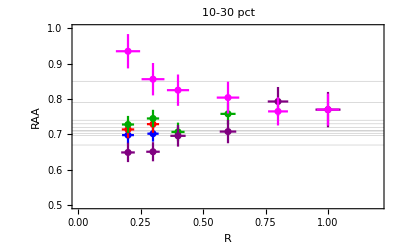

```mathematica
plot30=Show[{dat11,dat12,dat13,dat14,dat15},GridLines->{None,{{fit30c34[[1]]+fit30c34[[2]],{Darker[Green],Thick}},{fit30c34[[1]]-fit30c34[[2]],{Darker[Green],Thick}},{fit30c45[[1]]+fit30c45[[2]],{Purple,Thick}},{fit30c45[[1]]-fit30c45[[2]],{Purple,Thick}},{fit30c50[[1]]+fit30c50[[2]],{Magenta,Thick}},{fit30c50[[1]]-fit30c50[[2]],{Magenta,Thick}},{fit30c22[[1]]+fit30c22[[2]],{Blue,Thick}},{fit30c22[[1]]-fit30c22[[2]],{Blue,Thick}},{fit30c23[[1]]+fit30c23[[2]],{Red,Thick}},{fit30c23[[1]]-fit30c23[[2]],{Red,Thick}}}}]
```

```mathematica
plot50=Show[{dat21,dat22,dat23},GridLines->{None,{{fit50c34[[1]]+fit50c34[[2]],{Darker[Green],Thick}},{fit50c34[[1]]-fit50c34[[2]],{Darker[Green],Thick}},{fit50c22[[1]]+fit50c22[[2]],{Blue,Thick}},{fit50c22[[1]]-fit50c22[[2]],{Blue,Thick}},{fit50c23[[1]]+fit50c23[[2]],{Red,Thick}},{fit50c23[[1]]-fit50c23[[2]],{Red,Thick}}}}]
```

-Graphics-

```mathematica
plot90=Show[{dat31,dat32,dat33},GridLines->{None,{{fit90c34[[1]]+fit90c34[[2]],{Darker[Green],Thick}},{fit90c34[[1]]-fit90c34[[2]],{Darker[Green],Thick}},{fit90c22[[1]]+fit90c22[[2]],{Blue,Thick}},{fit90c22[[1]]-fit90c22[[2]],{Blue,Thick}},{fit90c23[[1]]+fit90c23[[2]],{Red,Thick}},{fit90c23[[1]]-fit90c23[[2]],{Red,Thick}}}}]
```

-Graphics-

```mathematica
Export["plot10.png",plot10];
Export["plot30.png",plot30];
Export["plot50.png",plot50];
Export["plot90.png",plot90];
```